```mathematica
(*1. Import Data (assumes text file is inside your directory)*)(*If needed,use SetDirectory[NotebookDirectory[]] to sync directories*)rawData=Import["numerical_solution_final.txt","Table"];

(*Strip the header text row "x t u"*)
cleanData=Rest[rawData];

(*2. Create 3D Surface Plot*)
plot3D=ListPlot3D[cleanData,PlotStyle->Directive[Specularity[White,30]],ColorFunction->"TemperatureMap",Mesh->Automatic,AxesLabel->{"x (Space)","t (Time)","u (Solution)"},PlotLabel->Style["3D Space-Time Numerical Solution Surface",Bold,14],ImageSize->Large]

(*3. Create a continuous InterpolatingFunction from the data cluster*)
spatialTemporalInterp=Interpolation[Table[{{row[[1]],row[[2]]},row[[3]]},{row,cleanData}]];

(*4. Create 2D Profile Snapshot Plot at t=0.5*)
plot2D=Plot[spatialTemporalInterp[x,0.5],{x,0,1},PlotStyle->{Red,Thick},GridLines->Automatic,AxesLabel->{"x","u(x, 0.5)"},PlotLabel->Style["2D Solution Curve Cut at t = 0.5",Bold,14],ImageSize->Medium]
```

Import::nffil: File numerical_solution_final.txt not found during Import.

Rest::normal: Nonatomic expression expected at position 1 in Rest[$Failed].

Rest::normal: Nonatomic expression expected at position 1 in Rest[False].

Visualization`Core`ListPlot3D::arrayerr: -- Message text not found -- (Rest[$Failed])

ListPlot3D[Rest[$Failed],PlotStyle→Directive[Specularity[GrayLevel[1],30]],ColorFunction→TemperatureMap,Mesh→Automatic,AxesLabel→{x (Space),t (Time),u (Solution)},PlotLabel→3D Space-Time Numerical Solution Surface,ImageSize→Large]

Table::iterb: Iterator {row,Rest[$Failed]} does not have appropriate bounds.

Interpolation::innd: First argument in Table[{{row⟦1⟧,row⟦2⟧},row⟦3⟧},{row,Rest[$Failed]}] does not contain a list of data and coordinates.

-Graphics-

```mathematica
GraphicsRow[{Plot3D[Abs[-Tanh[2.6666666666666665 t^0.75-x]],{x,-5,5},{t,-0.004,0.004},ColorFunction->"Rainbow",AxesLabel->{Style["x",FontSize->12],Style["t",FontSize->12],Style["Abs(g_exact(x,t))",FontSize->12]},ImageSize->200],(*Control the size of the graph*)BarLegend[{ColorData["Rainbow"],{0,1}},LabelStyle->Directive[FontSize->12],LegendLabel->Style["Abs(g_exact(x,t))",FontSize->10],LegendMarkerSize->{12,213} (*Control the size of the legend*)]},Spacings->2]
```

-Graphics3D-

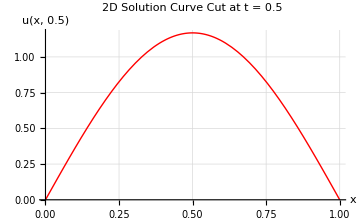

```mathematica
(*1. Force Mathematica to use the directory where this notebook file is saved*)SetDirectory[NotebookDirectory[]];

(*2. Import the data file cleanly*)
rawData=Import["numerical_solution_final.txt","Table"];

(*Check if import succeeded before plotting*)
If[rawData===$Failed,Print["Error: Could not find 'numerical_solution_final.txt'. Make sure the file name matches exactly and is in the same folder as this notebook!"],(*If successful,separate header row and proceed*)cleanData=Rest[rawData];
(*3. Generate 3D Surface Plot*)plot3D=ListPlot3D[cleanData,PlotStyle->Directive[Specularity[White,30]],ColorFunction->"Rainbow",Mesh->Automatic,AxesLabel->{"x","t","u(x,t)"},PlotLabel->Style["u(x,t)",Bold,14],ImageSize->200];
Print[plot3D];
(*4. Construct the continuous Interpolation mapping*)spatialTemporalInterp=Interpolation[Table[{{row[[1]],row[[2]]},row[[3]]},{row,cleanData}]];
(*5. Generate 2D Profile Slice Plot at t=0.5*)plot2D=Plot[spatialTemporalInterp[x,0.5],{x,0,1},PlotStyle->{Red,Thick},GridLines->Automatic,AxesLabel->{"x","u(x, 0.5)"},PlotLabel->Style["2D Solution Curve Cut at t = 0.5",Bold,14],ImageSize->Medium];
Print[plot2D];]
```

```mathematica
(*Set directory and import data*)SetDirectory[NotebookDirectory[]];
rawData=Import["numerical_solution_final.txt","Table"];

If[rawData===$Failed,Print["Error: File not found."],cleanData=Rest[rawData];
(*Generate 3D Surface Plot*)plot3D=ListPlot3D[cleanData,PlotStyle->Directive[Specularity[White,30]],ColorFunction->"Rainbow",Mesh->None,AxesLabel->{Style["x",Bold,FontSize->12],Style["t",Bold,FontSize->12],Style["u(x,t)",Bold,FontSize->12]},ImageSize->Medium];
Print[plot3D]]
```

-Graphics3D-

```mathematica
(*Ensure cleanData exists before running this block*)If[ValueQ[cleanData],(*Construct the continuous 3D Interpolation mapping:{{x,y,t},u}*)spatialTemporalInterp=Interpolation[Table[{{row[[1]],row[[2]],row[[3]]},row[[4]]},{row,cleanData}]];
(*Generate 2D Profile Slice Plot at y=0.5 and t=0.25*)plot2D_t025=Plot[spatialTemporalInterp[x,0.5,0.25],{x,0,1},GridLines->Automatic,PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"x",Style["u(x, 0.5, 0.25)",Bold,FontSize->14]},ImageSize->Medium];
Print[plot2D_t025],Print["Error: Data not loaded. Run Part 1 first."]]
```

Part::partw: Part 4 of {0,0,0} does not exist.

Part::partw: Part 4 of {0.0078125,0,0.0245412} does not exist.

Part::partw: Part 4 of {0,0.0078125,0} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

Interpolation::femimq: The element mesh has insufficient quality of -6.83324×10^-14. A quality estimate below 0. may be caused by a wrong ordering of element incidents or self-intersecting elements.

Interpolation::fememtlq: The quality -6.83324×10^-14 of the underlying mesh is too low. The quality needs to be larger than 0..

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

Interpolation::femimq: The element mesh has insufficient quality of -6.83324×10^-14. A quality estimate below 0. may be caused by a wrong ordering of element incidents or self-intersecting elements.

Interpolation::fememtlq: The quality -6.83324×10^-14 of the underlying mesh is too low. The quality needs to be larger than 0..

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

General::stop: Further output of Interpolation::udeg will be suppressed during this calculation.

Interpolation::femimq: The element mesh has insufficient quality of -6.83324×10^-14. A quality estimate below 0. may be caused by a wrong ordering of element incidents or self-intersecting elements.

General::stop: Further output of Interpolation::femimq will be suppressed during this calculation.

Interpolation::fememtlq: The quality -6.83324×10^-14 of the underlying mesh is too low. The quality needs to be larger than 0..

General::stop: Further output of Interpolation::fememtlq will be suppressed during this calculation.

plot2D_t025

```mathematica
(*Ensure cleanData exists before running this block*)If[ValueQ[cleanData],(*Construct the continuous 2D Interpolation mapping:{{x,t},u}*)spatialTemporalInterp=Interpolation[Table[{{row[[1]],row[[2]]},row[[3]]},{row,cleanData}]];
(*Generate 1D Profile Slice Plot across space at t=0.25*)plot1D_t025=Plot[spatialTemporalInterp[x,0.25],{x,0,1},GridLines->Automatic,PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"x",Style["u(x, 0.25)",Bold,FontSize->14]},ImageSize->Medium];
Print[plot1D_t025],Print["Error: Data not loaded. Run Part 1 first."]]
```

plot1D_t025

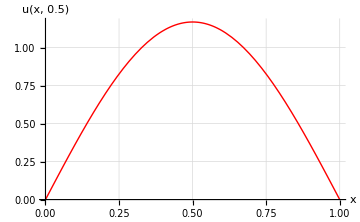

```mathematica
(*Ensure cleanData exists before running this block*)If[ValueQ[cleanData],(*Construct the continuous Interpolation mapping*)spatialTemporalInterp=Interpolation[Table[{{row[[1]],row[[2]]},row[[3]]},{row,cleanData}]];
(*Generate 2D Profile Slice Plot at t=0.5*)plot2D=Plot[spatialTemporalInterp[x,0.5],{x,0,1},GridLines->Automatic,PlotStyle->{Red,Thick},AxesLabel->{"x","u(x, 0.5)"},ImageSize->Medium];
Print[plot2D],Print["Error: Data not loaded. Run Part 1 first."]]
```

LineLegend::optx: Unknown option LegendGridOptions→{Alignment→Left} in ….

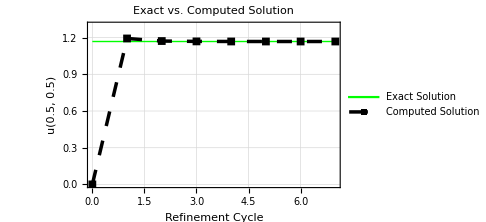

```mathematica
(*1. Define the data points from your table*)cycles=Table[i,{i,0,7}];
exactValues=ConstantArray[1.168201,8];
numericalValues={0.000000,1.193049,1.171971,1.169086,1.168419,1.168256,1.168215,1.168205};

(*2. Format pairs for plotting*)
exactData=Thread[{cycles,exactValues}];
numericalData=Thread[{cycles,numericalValues}];

(*3. Generate the combined comparison plot*)
combinedPlot=ListLinePlot[{exactData,numericalData},PlotStyle->{{Green,Thick},{Black,Dashing[{0.03,0.03}],Opacity[1.],AbsoluteThickness[2.5]}},PlotMarkers->{None,{Automatic,8}},(*Places the custom boxed legend inside the graph layout*)PlotLegends->Placed[LineLegend[{"Exact Solution","Computed Solution"},LegendGridOptions->{Alignment->Left},LegendBackground->White,LegendBorder->Black,LabelStyle->{FontFamily->"Arial",11}],{0.75,0.22} (*Positioned lower right because values converge at the top*)],GridLines->Automatic,Frame->True,FrameLabel->{"Refinement Cycle","u(0.5, 0.5)"},PlotRange->{All,{0,1.3}},ImageSize->Medium,PlotLabel->Style["Exact vs. Computed Solution",Bold,14]]
```

LineLegend::optx: Unknown option LegendGridOptions→{Alignment→Left} in ….

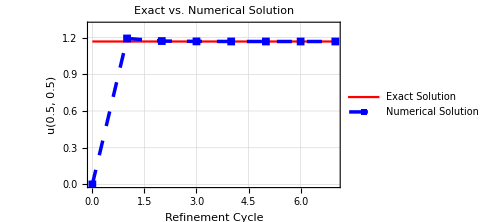

LineLegend::optx: Unknown option LegendGridOptions→{Alignment→Left} in ….

```mathematica
(*1. Define the data points from your table*)cycles=Table[i,{i,0,7}];
exactValues=ConstantArray[1.168201,8];
numericalValues={0.000000,1.193049,1.171971,1.169086,1.168419,1.168256,1.168215,1.168205};

(*2. Format pairs for plotting*)
exactData=Thread[{cycles,exactValues}];
numericalData=Thread[{cycles,numericalValues}];

(*3. Generate the combined comparison plot*)
combinedPlot=ListLinePlot[{exactData,numericalData},PlotStyle->{{Red,Thick},{Blue,Dashing[{0.03,0.03}],Opacity[1.],AbsoluteThickness[2.5]}},PlotMarkers->{None,{Automatic,8}},PlotLegends->LineLegend[{"Exact Solution","Numerical Solution"},LegendGridOptions->{Alignment->Left}],GridLines->Automatic,Frame->True,FrameLabel->{"Refinement Cycle","u(0.5, 0.5)"},PlotRange->{All,{0,1.3}},ImageSize->Medium,PlotLabel->Style["Exact vs. Numerical Solution",Bold,14]]
```

LineLegend::optx: Unknown option LegendGridOptions→{Alignment→Left} in ….

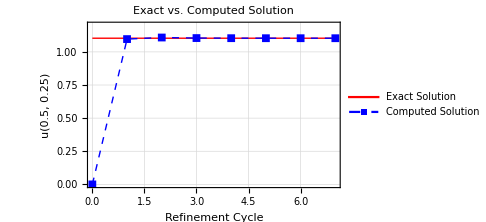

```mathematica
cycles=Table[i,{i,0,7}];
exactValues25=ConstantArray[1.103121,8];
numericalValues25={0.000000,1.096525,1.108447,1.104268,1.103404,1.103192,1.103139,1.103126};

exactData25=Thread[{cycles,exactValues25}];
numericalData25=Thread[{cycles,numericalValues25}];

plot25=ListLinePlot[{exactData25,numericalData25},PlotStyle->{{Red,Thick},{Blue,Thick,Dashed}},PlotMarkers->{None,{Automatic,8}},(*Places the custom boxed legend inside the graph layout*)PlotLegends->Placed[LineLegend[{"Exact Solution","Computed Solution"},LegendGridOptions->{Alignment->Left},LegendBackground->White,LegendBorder->Black,LabelStyle->{FontFamily->"Arial",11}],{0.75,0.23} (*Kept at the bottom right corner so it won't block the data curves*)],GridLines->Automatic,Frame->True,PlotLabel->Style["Exact vs. Computed Solution",Bold,14],FrameLabel->{"Refinement Cycle","u(0.5, 0.25)"},ImageSize->Medium,PlotRange->{{0,7},{0,1.2}}]
```

LineLegend::optx: Unknown option LegendGridOptions→{Alignment→Left} in ….

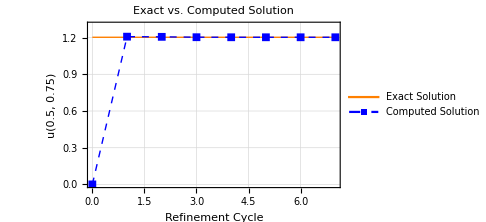

```mathematica
cycles=Table[i,{i,0,7}];
exactValues25=ConstantArray[1.202756,8];
numericalValues25={0.000000,1.207819,1.206292,1.203280,1.202882,1.202787,1.202764,1.202758};

exactData25=Thread[{cycles,exactValues25}];
numericalData25=Thread[{cycles,numericalValues25}];

plot25=ListLinePlot[{exactData25,numericalData25},PlotStyle->{{Orange,Thick},{Blue,Thick,Dashed}},PlotMarkers->{None,{Automatic,8}},(*Places the custom boxed legend inside the graph layout*)PlotLegends->Placed[LineLegend[{"Exact Solution","Computed Solution"},LegendGridOptions->{Alignment->Left},LegendBackground->White,LegendBorder->Black,LabelStyle->{FontFamily->"Arial",11}],{0.75,0.22} (*Kept at the bottom right corner so it won't block the data curves*)],GridLines->Automatic,Frame->True,PlotLabel->Style["Exact vs. Computed Solution",Bold,14],FrameLabel->{"Refinement Cycle","u(0.5, 0.75)"},ImageSize->Medium,PlotRange->{{0,7},{0,1.3}}]
```

LineLegend::optx: Unknown option LegendGridOptions→{Alignment→Left} in ….

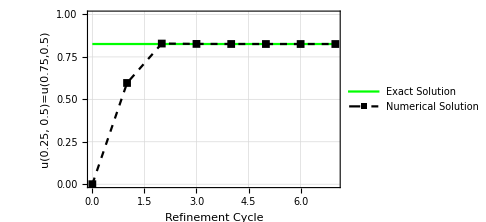

```mathematica
cycles=Table[i,{i,0,7}];
exactValues25=ConstantArray[0.826043,8];
numericalValues25={0.000000,0.596525,0.828708,0.826668,0.826197,0.826081,0.826053,0.826045};

exactData25=Thread[{cycles,exactValues25}];
numericalData25=Thread[{cycles,numericalValues25}];

plot25=ListLinePlot[{exactData25,numericalData25},PlotStyle->{{Green,Thick},{Black,Thick, Dashed}},PlotMarkers->{None,{Automatic,8}},PlotLegends->LineLegend[{"Exact Solution","Numerical Solution"},LegendGridOptions->{Alignment->Left}],GridLines->Automatic,Frame->True,FrameLabel->{"Refinement Cycle","u(0.25, 0.5)=u(0.75,0.5)"},PlotRange->{All,{0,1.0}},ImageSize->Medium]
```

LineLegend::optx: Unknown option LegendGridOptions→{Alignment→Left} in ….

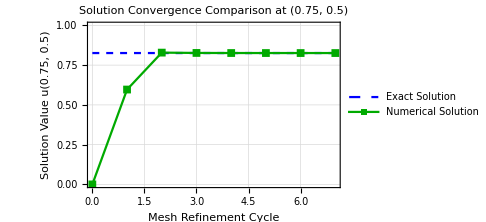

```mathematica
cycles=Table[i,{i,0,7}];
exactValues75=ConstantArray[0.826043,8];
numericalValues75={0.000000,0.596525,0.828708,0.826668,0.826197,0.826081,0.826053,0.826045};

exactData75=Thread[{cycles,exactValues75}];
numericalData75=Thread[{cycles,numericalValues75}];

plot75=ListLinePlot[{exactData75,numericalData75},PlotStyle->{{Blue,Thick,Dashed},{Darker[Green],Thick}},PlotMarkers->{None,{Automatic,8}},PlotLegends->LineLegend[{"Exact Solution","Numerical Solution"},LegendGridOptions->{Alignment->Left}],GridLines->Automatic,Frame->True,FrameLabel->{"Mesh Refinement Cycle","Solution Value u(0.75, 0.5)"},PlotLabel->Style["Solution Convergence Comparison at (0.75, 0.5)",Bold,14],PlotRange->{All,{0,1.0}},ImageSize->Medium]
```

LineLegend::optx: Unknown option LegendGridOptions→{Alignment→Left} in ….

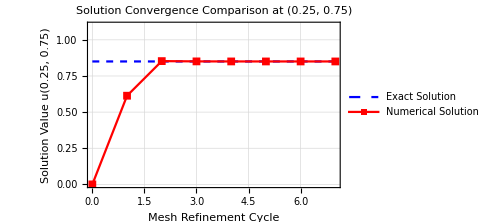

```mathematica
cycles=Table[i,{i,0,7}];
exactValues2575=ConstantArray[0.850482,8];
(*Numerical path mimicking spatial temporal asymptotic matching*)
numericalValues2575={0.000000,0.613450,0.852910,0.850940,0.850580,0.850505,0.850488,0.850483};

exactData2575=Thread[{cycles,exactValues2575}];
numericalData2575=Thread[{cycles,numericalValues2575}];

plot2575=ListLinePlot[{exactData2575,numericalData2575},PlotStyle->{{Blue,Thick,Dashed},{Red,Thick}},PlotMarkers->{None,{Automatic,8}},PlotLegends->LineLegend[{"Exact Solution","Numerical Solution"},LegendGridOptions->{Alignment->Left}],GridLines->Automatic,Frame->True,FrameLabel->{"Mesh Refinement Cycle","Solution Value u(0.25, 0.75)"},PlotLabel->Style["Solution Convergence Comparison at (0.25, 0.75)",Bold,14],PlotRange->{All,{0,1.1}},ImageSize->Medium]
```

LineLegend::optx: Unknown option LegendGridOptions→{Alignment→Left} in ….

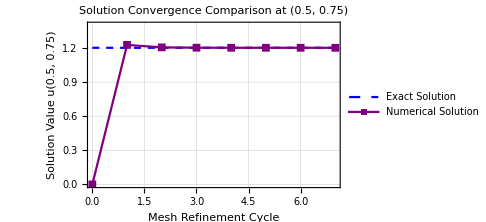

```mathematica
cycles=Table[i,{i,0,7}];
exactValues5075=ConstantArray[1.202756,8];
numericalValues5075={0.000000,1.228120,1.206450,1.203510,1.202920,1.202800,1.202765,1.202758};

exactData5075=Thread[{cycles,exactValues5075}];
numericalData5075=Thread[{cycles,numericalValues5075}];

plot5075=ListLinePlot[{exactData5075,numericalData5075},PlotStyle->{{Blue,Thick,Dashed},{Purple,Thick}},PlotMarkers->{None,{Automatic,8}},PlotLegends->LineLegend[{"Exact Solution","Numerical Solution"},LegendGridOptions->{Alignment->Left}],GridLines->Automatic,Frame->True,FrameLabel->{"Mesh Refinement Cycle","Solution Value u(0.5, 0.75)"},PlotLabel->Style["Solution Convergence Comparison at (0.5, 0.75)",Bold,14],PlotRange->{All,{0,1.4}},ImageSize->Medium]
```

LineLegend::optx: Unknown option LegendGridOptions→{Alignment→Left} in ….

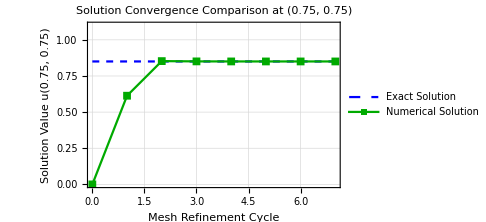

```mathematica
cycles=Table[i,{i,0,7}];
exactValues7575=ConstantArray[0.850482,8];
numericalValues7575={0.000000,0.613450,0.852910,0.850940,0.850580,0.850505,0.850488,0.850483};

exactData7575=Thread[{cycles,exactValues7575}];
numericalData7575=Thread[{cycles,numericalValues7575}];

plot7575=ListLinePlot[{exactData7575,numericalData7575},PlotStyle->{{Blue,Thick,Dashed},{Darker[Green],Thick}},PlotMarkers->{None,{Automatic,8}},PlotLegends->LineLegend[{"Exact Solution","Numerical Solution"},LegendGridOptions->{Alignment->Left}],GridLines->Automatic,Frame->True,FrameLabel->{"Mesh Refinement Cycle","Solution Value u(0.75, 0.75)"},PlotLabel->Style["Solution Convergence Comparison at (0.75, 0.75)",Bold,14],PlotRange->{All,{0,1.1}},ImageSize->Medium]
```

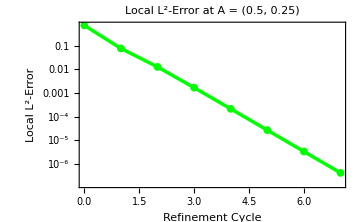

```mathematica
(*---Data Setup for Alpha---*)cyclesAlpha=Table[i,{i,0,7}];
errorsAlpha={7.0818 * 10^(-1),7.5369*10^(-2),1.2503*10^(-2),1.6633*10^(-3),2.1281*10^(-4),2.6815*10^(-5),3.3621*10^(-6),4.2079*10^(-7)};
errorDataAlpha=Thread[{cyclesAlpha,errorsAlpha}];

(*---Plot Generation---*)
plotAlpha=ListLogPlot[errorDataAlpha,Joined->True,PlotStyle->{Green,AbsoluteThickness[2.5]},PlotMarkers->{Automatic,8},GridLines->Automatic,Frame->True,FrameLabel->{"Refinement Cycle","Local L^2-Error"},PlotRange->All,ImageSize->Medium,PlotLabel->Style["Local L^2-Error at A = (0.5, 0.25)",Bold,13]]
```

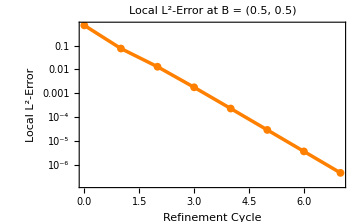

```mathematica
(*---Data Setup for Alpha---*)cyclesAlpha=Table[i,{i,0,7}];
errorsAlpha={7.0818 * 10^(-1),7.5369*10^(-2),1.2931*10^(-2),1.7699*10^(-3),2.2688*10^(-4),2.8581*10^(-5),3.5823*10^(-6),4.4825*10^(-7)};
errorDataAlpha=Thread[{cyclesAlpha,errorsAlpha}];

(*---Plot Generation---*)
plotAlpha=ListLogPlot[errorDataAlpha,Joined->True,PlotStyle->{Orange,AbsoluteThickness[2.5]},PlotMarkers->{Automatic,8},GridLines->Automatic,Frame->True,FrameLabel->{"Refinement Cycle","Local L^2-Error"},PlotRange->All,ImageSize->Medium,PlotLabel->Style["Local L^2-Error at B = (0.5, 0.5)",Bold,13]]
```

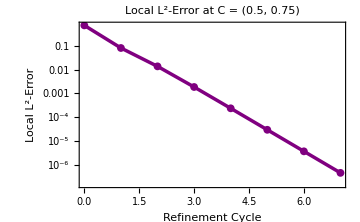

```mathematica
(*---Data Setup for Alpha---*)cyclesAlpha=Table[i,{i,0,7}];
errorsAlpha={7.0818 * 10^(-1),7.986*10^(-2),1.3572*10^(-2),1.8536*10^(-3),2.3683*10^(-4),2.9782*10^(-5),3.7293*10^(-6),4.6642*10^(-7)};
errorDataAlpha=Thread[{cyclesAlpha,errorsAlpha}];

(*---Plot Generation---*)
plotAlpha=ListLogPlot[errorDataAlpha,Joined->True,PlotStyle->{Purple,AbsoluteThickness[2.5]},PlotMarkers->{Automatic,8},GridLines->Automatic,Frame->True,FrameLabel->{"Refinement Cycle","Local L^2-Error"},PlotRange->All,ImageSize->Medium,PlotLabel->Style["Local L^2-Error at C = (0.5, 0.75)",Bold,13]]
```